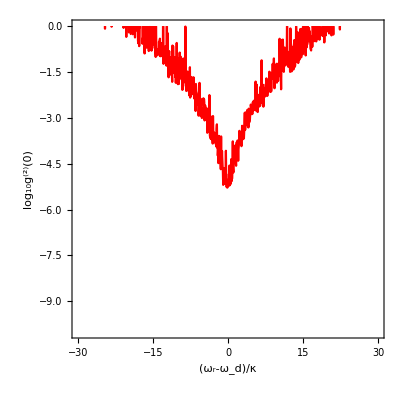

```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[100];



data=ParallelTable[
ωr=4*2*Pi;
ωq=8*2*Pi;
Na=10;


γ=0.001*ωr;
κ=0.001*ωr;
E1=3*κ;
max1=30*κ;
min1=-30*κ;      (*max and min value of Δ*)
segment1=1000;

Δ=N[min1+(max1-min1)*(m-1)/segment1];(*m is the variable of Δ for circulation*)
(*Δ=ωr-ωd*)
C1=√(E1^2/(2 E1^2+4 Δ^2+κ^2));
ωqdeviation=10^-5*ωq;
gdelta=RandomReal[{0,0.02*ωr},Na];
deltadata=RandomReal[NormalDistribution[ωq,ωqdeviation],Na]-ωq;

equs=Table[{deltadata[[i]]*ToExpression[StringJoin["C2",ToString[i]]]+gdelta[[i]]*C2*√2+E1/2*ToExpression[StringJoin["C3",ToString[i]]]-I/2*γ*ToExpression[StringJoin["C2",ToString[i]]]+2*Δ*ToExpression[StringJoin["C2",ToString[i]]]==0,deltadata[[i]]*ToExpression[StringJoin["C3",ToString[i]]]+gdelta[[i]]*C3*√6+E1/2*ToExpression[StringJoin["C2",ToString[i]]]-I/2*κ*ToExpression[StringJoin["C3",ToString[i]]]-I/2*γ*ToExpression[StringJoin["C3",ToString[i]]]+Δ*ToExpression[StringJoin["C3",ToString[i]]]+2*Δ*ToExpression[StringJoin["C3",ToString[i]]]==0},{i,1,Na}];
equs=Flatten[equs];
equs=Append[equs,(Sum[gdelta[[i]]*√2*ToExpression[StringJoin["C2",ToString[i]]],{i,Na}])+E1/2*C1*√2+E1/2*C3*√3-I*κ*C2+2*Δ*C2==0];
equs=Append[equs,(Sum[gdelta[[i]]*√6*ToExpression[StringJoin["C3",ToString[i]]],{i,Na}])+E1/2*C2*√3-I/2*κ*C3*3+3*Δ*C3==0];

vars={C2,C3,Table[ToExpression[StringJoin["C2",ToString[i]]],{i,1,Na}],Table[ToExpression[StringJoin["C3",ToString[i]]],{i,1,Na}]};
vars=Flatten[vars];
S=NSolve[equs,vars];
C2data=C2/.S[[1,1]];
C3data=C3/.S[[1,2]];
logg20=Log10[(Abs[C2data]^2*2+Abs[C3data]^2*6)/((E1^2/(2 E1^2+4 Δ^2+κ^2))^2)];


{Δ/κ,logg20},{m,1,1000+1,1},Method->"FinestGrained"

];
(*Circulation is ended.*)


ListPlot[data,FrameLabel->{"(ω_c-ω_d)/κ","log_10g^(2)(0)"},BaseStyle->{FontSize->26,FontFamily->"Calibri"},Joined->True,PlotStyle->{Red},Frame->True,PlotRange->{{-30,30},{-10,0}},AspectRatio->1]
```

```mathematica
datalist=Import["/home/u000011703749/2photonJ-Cdeltag&deltaz.txt","Table"];
datalist=Join[datalist,data];
Export["/home/u000011703749/2photonJ-Cdeltag&deltaz.txt",datalist,"Table"];
```

```mathematica
datalist
```

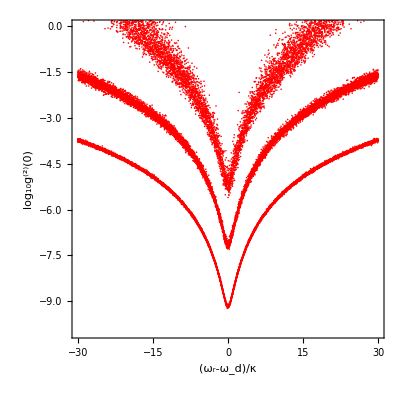

```mathematica
datalist=Import["/home/u000011703749/2photonJ-Cdeltag&deltaz.txt","Table"];
ListPlot[datalist,FrameLabel->{"(ω_r-ω_d)/κ","log_10g^(2)(0)"},BaseStyle->{FontSize->26,FontFamily->"Calibri"},Joined->False,PlotStyle->{Red},Frame->True,PlotRange->{{-30,30},{-10,0}},AspectRatio->1]
```

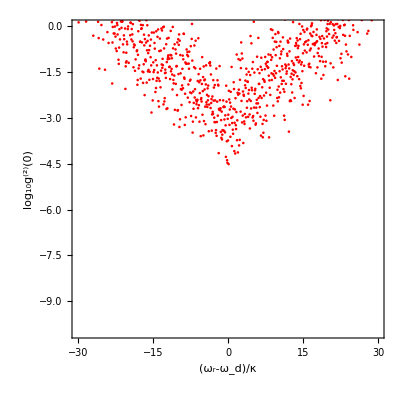

```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[100];



data=ParallelTable[
ωr=4*2*Pi;
ωq=8*2*Pi;
Na=10;


γ=0.001*ωr;
κ=0.001*ωr;
E1=3*κ;
max1=30*κ;
min1=-30*κ;      (*max and min value of Δ*)
segment1=1000;

Δ=N[min1+(max1-min1)*(m-1)/segment1];(*m is the variable of Δ for circulation*)
(*Δ=ωr-ωd*)
C1=√(E1^2/(2 E1^2+4 Δ^2+κ^2));
ωqdeviation=10^-2*ωq;
gdelta=RandomReal[{0,0.02*ωr},Na];
deltadata=RandomReal[NormalDistribution[ωq,ωqdeviation],Na]-ωq;

equs=Table[{deltadata[[i]]*ToExpression[StringJoin["C2",ToString[i]]]+gdelta[[i]]*C2*√2+E1/2*ToExpression[StringJoin["C3",ToString[i]]]-I/2*γ*ToExpression[StringJoin["C2",ToString[i]]]+2*Δ*ToExpression[StringJoin["C2",ToString[i]]]==0,deltadata[[i]]*ToExpression[StringJoin["C3",ToString[i]]]+gdelta[[i]]*C3*√6+E1/2*ToExpression[StringJoin["C2",ToString[i]]]-I/2*κ*ToExpression[StringJoin["C3",ToString[i]]]-I/2*γ*ToExpression[StringJoin["C3",ToString[i]]]+Δ*ToExpression[StringJoin["C3",ToString[i]]]+2*Δ*ToExpression[StringJoin["C3",ToString[i]]]==0},{i,1,Na}];
equs=Flatten[equs];
equs=Append[equs,(Sum[gdelta[[i]]*√2*ToExpression[StringJoin["C2",ToString[i]]],{i,Na}])+E1/2*C1*√2+E1/2*C3*√3-I*κ*C2+2*Δ*C2==0];
equs=Append[equs,(Sum[gdelta[[i]]*√6*ToExpression[StringJoin["C3",ToString[i]]],{i,Na}])+E1/2*C2*√3-I/2*κ*C3*3+3*Δ*C3==0];

vars={C2,C3,Table[ToExpression[StringJoin["C2",ToString[i]]],{i,1,Na}],Table[ToExpression[StringJoin["C3",ToString[i]]],{i,1,Na}]};
vars=Flatten[vars];
S=NSolve[equs,vars];
C2data=C2/.S[[1,1]];
C3data=C3/.S[[1,2]];
logg20=Log10[(Abs[C2data]^2*2+Abs[C3data]^2*6)/((E1^2/(2 E1^2+4 Δ^2+κ^2))^2)];


{Δ/κ,logg20},{m,1,1000+1,1},Method->"FinestGrained"

];
(*Circulation is ended.*)


ListPlot[data,FrameLabel->{"(ω_r-ω_d)/κ","log_10g^(2)(0)"},BaseStyle->{FontSize->26,FontFamily->"Calibri"},Joined->False,PlotStyle->{Red},Frame->True,PlotRange->{{-30,30},{-10,0}},AspectRatio->1]
```

```mathematica
datalist=Import["/home/u000011703749/2photonJ-Cdeltag&deltaz-2.txt","Table"];
datalist=Join[datalist,data];
Export["/home/u000011703749/2photonJ-Cdeltag&deltaz-2.txt",datalist,"Table"];
```

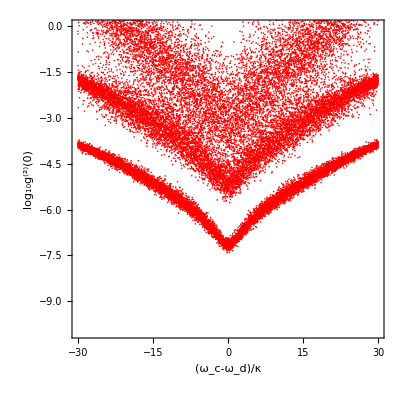

```mathematica
datalist=Import["/home/u000011703749/2photonJ-Cdeltag&deltaz-2.txt","Table"];
ListPlot[datalist,FrameLabel->{"(ω_c-ω_d)/κ","log_10g^(2)(0)"},BaseStyle->{FontSize->20,FontFamily->"Calibri"},Joined->False,PlotStyle->{Red},Frame->True,PlotRange->{{-30,30},{-10,0}},AspectRatio->1]
```

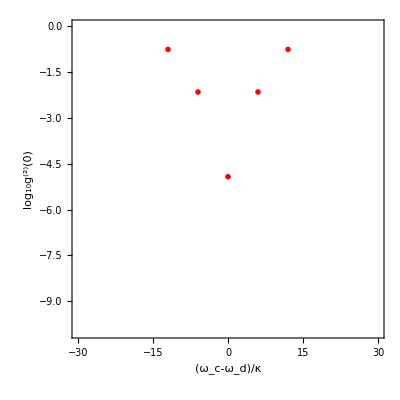
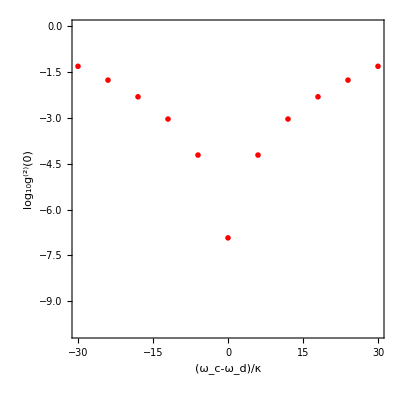
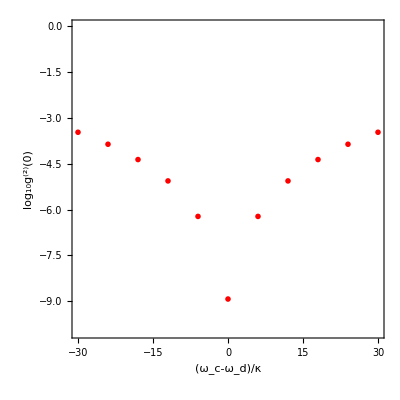
```mathematica
Show[-Graphics-,-Graphics-,-Graphics-,-Graphics-]
```

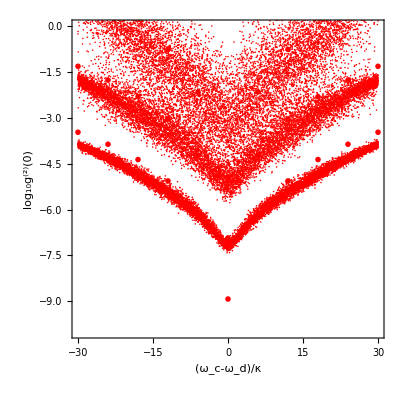

```mathematica
Export["/home/u000011703749/figs1b.pdf",-Graphics-]
```

/home/u000011703749/figs1b.pdf

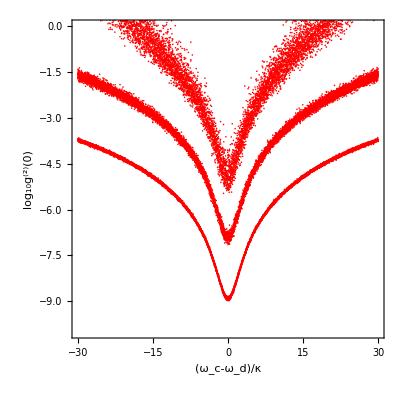
```mathematica
Show[-Graphics-,-Graphics-,-Graphics-,-Graphics-]
```

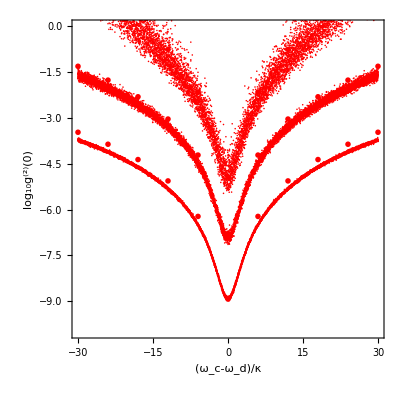

```mathematica
Export["/home/u000011703749/figs1a.pdf",-Graphics-]
```

/home/u000011703749/figs1a.pdf

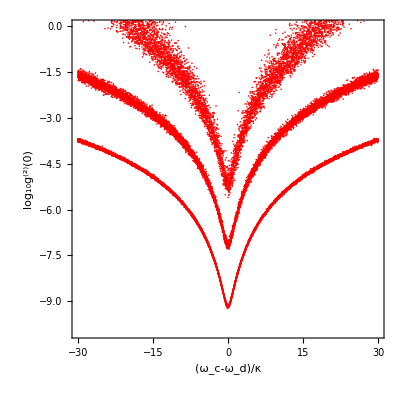

```mathematica
datalist=Import["/home/u000011703749/2photonJ-Cdeltag&deltaz-5.txt","Table"];
ListPlot[datalist,FrameLabel->{"(ω_c-ω_d)/κ","log_10g^(2)(0)"},BaseStyle->{FontSize->20,FontFamily->"Calibri"},Joined->False,PlotStyle->{Red},Frame->True,PlotRange->{{-30,30},{-10,0}},AspectRatio->1]
```

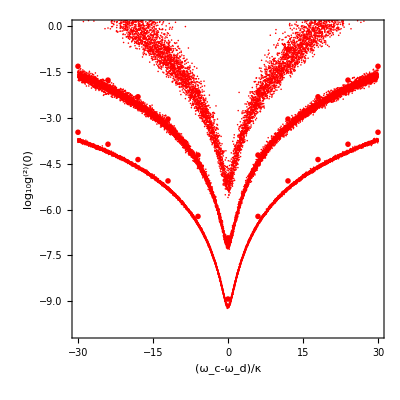

```mathematica
Show[-Graphics-,-Graphics-,-Graphics-,-Graphics-]
```

```mathematica
Export["/home/u000011703749/figs1a.eps",-Graphics-]
```

/home/u000011703749/figs1a.eps

```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[100];



data=ParallelTable[
ωr=4*2*Pi;
ωq=8*2*Pi;
Na=1000;


γ=0.001*ωr;
κ=0.001*ωr;
E1=3*κ;
max1=30*κ;
min1=-30*κ;      (*max and min value of Δ*)
segment1=10;

Δ=N[min1+(max1-min1)*(m-1)/segment1];(*m is the variable of Δ for circulation*)
(*Δ=ωr-ωd*)
C1=√(E1^2/(2 E1^2+4 Δ^2+κ^2));

g=0.01*ωr;


equs=Table[{g*C2*√2+E1/2*ToExpression[StringJoin["C3",ToString[i]]]-I/2*γ*ToExpression[StringJoin["C2",ToString[i]]]+2*Δ*ToExpression[StringJoin["C2",ToString[i]]]==0,g*C3*√6+E1/2*ToExpression[StringJoin["C2",ToString[i]]]-I/2*κ*ToExpression[StringJoin["C3",ToString[i]]]-I/2*γ*ToExpression[StringJoin["C3",ToString[i]]]+Δ*ToExpression[StringJoin["C3",ToString[i]]]+2*Δ*ToExpression[StringJoin["C3",ToString[i]]]==0},{i,1,Na}];
equs=Flatten[equs];
equs=Append[equs,(Sum[g*√2*ToExpression[StringJoin["C2",ToString[i]]],{i,Na}])+E1/2*C1*√2+E1/2*C3*√3-I*κ*C2+2*Δ*C2==0];
equs=Append[equs,(Sum[g*√6*ToExpression[StringJoin["C3",ToString[i]]],{i,Na}])+E1/2*C2*√3-I/2*κ*C3*3+3*Δ*C3==0];

vars={C2,C3,Table[ToExpression[StringJoin["C2",ToString[i]]],{i,1,Na}],Table[ToExpression[StringJoin["C3",ToString[i]]],{i,1,Na}]};
vars=Flatten[vars];
S=NSolve[equs,vars];
C2data=C2/.S[[1,1]];
C3data=C3/.S[[1,2]];
logg20=Log10[(Abs[C2data]^2*2+Abs[C3data]^2*6)/((E1^2/(2 E1^2+4 Δ^2+κ^2))^2)];


{Δ/κ,logg20},{m,1,10+1,1},Method->"FinestGrained"

];
(*Circulation is ended.*)


ListPlot[data,FrameLabel->{"(ω_c-ω_d)/κ","log_10g^(2)(0)"},BaseStyle->{FontSize->20,FontFamily->"Calibri"},Joined->False,PlotStyle->{Red},PlotMarkers->"OpenMarkers",Frame->True,PlotRange->{{-30,30},{-10,0}},AspectRatio->1]
```

-Graphics-

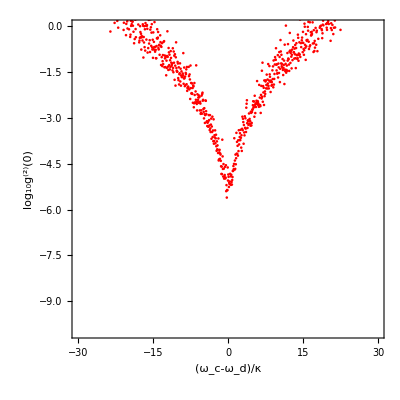

```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[100];



data=ParallelTable[
ωr=4*2*Pi;
ωq=8*2*Pi;
Na=10;


γ=0.001*ωr;
κ=0.001*ωr;
E1=3*κ;
max1=30*κ;
min1=-30*κ;      (*max and min value of Δ*)
segment1=1000;

Δ=N[min1+(max1-min1)*(m-1)/segment1];(*m is the variable of Δ for circulation*)
(*Δ=ωr-ωd*)
C1=√(E1^2/(2 E1^2+4 Δ^2+κ^2));
ωqdeviation=10^-5*ωq;
gdelta=RandomReal[{0,0.02*ωr},Na];
deltadata=RandomReal[NormalDistribution[ωq,ωqdeviation],Na]-ωq;

equs=Table[{deltadata[[i]]*ToExpression[StringJoin["C2",ToString[i]]]+gdelta[[i]]*C2*√2+E1/2*ToExpression[StringJoin["C3",ToString[i]]]-I/2*γ*ToExpression[StringJoin["C2",ToString[i]]]+2*Δ*ToExpression[StringJoin["C2",ToString[i]]]==0,deltadata[[i]]*ToExpression[StringJoin["C3",ToString[i]]]+gdelta[[i]]*C3*√6+E1/2*ToExpression[StringJoin["C2",ToString[i]]]-I/2*κ*ToExpression[StringJoin["C3",ToString[i]]]-I/2*γ*ToExpression[StringJoin["C3",ToString[i]]]+Δ*ToExpression[StringJoin["C3",ToString[i]]]+2*Δ*ToExpression[StringJoin["C3",ToString[i]]]==0},{i,1,Na}];
equs=Flatten[equs];
equs=Append[equs,(Sum[gdelta[[i]]*√2*ToExpression[StringJoin["C2",ToString[i]]],{i,Na}])+E1/2*C1*√2+E1/2*C3*√3-I*κ*C2+2*Δ*C2==0];
equs=Append[equs,(Sum[gdelta[[i]]*√6*ToExpression[StringJoin["C3",ToString[i]]],{i,Na}])+E1/2*C2*√3-I/2*κ*C3*3+3*Δ*C3==0];

vars={C2,C3,Table[ToExpression[StringJoin["C2",ToString[i]]],{i,1,Na}],Table[ToExpression[StringJoin["C3",ToString[i]]],{i,1,Na}]};
vars=Flatten[vars];
S=NSolve[equs,vars];
C2data=C2/.S[[1,1]];
C3data=C3/.S[[1,2]];
logg20=Log10[(Abs[C2data]^2*2+Abs[C3data]^2*6)/((E1^2/(2 E1^2+4 Δ^2+κ^2))^2)];


{Δ/κ,logg20},{m,1,1000+1,1},Method->"FinestGrained"

];
(*Circulation is ended.*)


ListPlot[data,FrameLabel->{"(ω_c-ω_d)/κ","log_10g^(2)(0)"},BaseStyle->{FontSize->20,FontFamily->"Calibri"},Joined->False,PlotStyle->{Red},Frame->True,PlotRange->{{-30,30},{-10,0}},AspectRatio->1]
```

```mathematica
datalist=Import["/home/u000011703749/2photonJ-Cdeltag&deltaz-5E3.txt","Table"];
datalist=Join[datalist,data];
Export["/home/u000011703749/2photonJ-Cdeltag&deltaz-5E3.txt",datalist,"Table"];
```

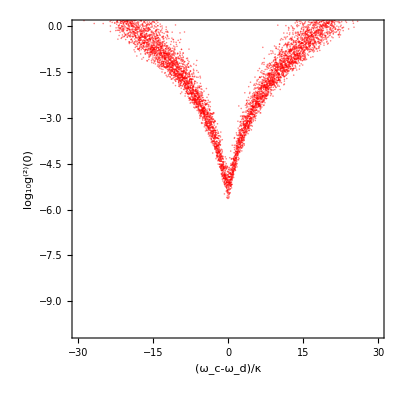

```mathematica
datalist=Import["/home/u000011703749/2photonJ-Cdeltag&deltaz-5E3.txt","Table"];
ListPlot[datalist,FrameLabel->{"(ω_c-ω_d)/κ","log_10g^(2)(0)"},BaseStyle->{FontSize->20,FontFamily->"Calibri"},Joined->False,PlotStyle->{Red,Opacity->0.5},Frame->True,PlotRange->{{-30,30},{-10,0}},AspectRatio->1]
```

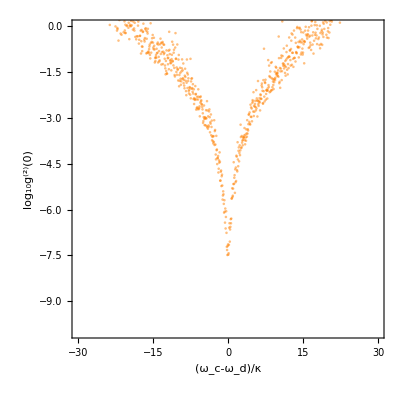

```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[100];



data=ParallelTable[
ωr=4*2*Pi;
ωq=8*2*Pi;
Na=10;


γ=0.001*ωr;
κ=0.001*ωr;
E1=0.3*κ;
max1=30*κ;
min1=-30*κ;      (*max and min value of Δ*)
segment1=1000;

Δ=N[min1+(max1-min1)*(m-1)/segment1];(*m is the variable of Δ for circulation*)
(*Δ=ωr-ωd*)
C1=√(E1^2/(2 E1^2+4 Δ^2+κ^2));
ωqdeviation=10^-5*ωq;
gdelta=RandomReal[{0,0.02*ωr},Na];
deltadata=RandomReal[NormalDistribution[ωq,ωqdeviation],Na]-ωq;

equs=Table[{deltadata[[i]]*ToExpression[StringJoin["C2",ToString[i]]]+gdelta[[i]]*C2*√2+E1/2*ToExpression[StringJoin["C3",ToString[i]]]-I/2*γ*ToExpression[StringJoin["C2",ToString[i]]]+2*Δ*ToExpression[StringJoin["C2",ToString[i]]]==0,deltadata[[i]]*ToExpression[StringJoin["C3",ToString[i]]]+gdelta[[i]]*C3*√6+E1/2*ToExpression[StringJoin["C2",ToString[i]]]-I/2*κ*ToExpression[StringJoin["C3",ToString[i]]]-I/2*γ*ToExpression[StringJoin["C3",ToString[i]]]+Δ*ToExpression[StringJoin["C3",ToString[i]]]+2*Δ*ToExpression[StringJoin["C3",ToString[i]]]==0},{i,1,Na}];
equs=Flatten[equs];
equs=Append[equs,(Sum[gdelta[[i]]*√2*ToExpression[StringJoin["C2",ToString[i]]],{i,Na}])+E1/2*C1*√2+E1/2*C3*√3-I*κ*C2+2*Δ*C2==0];
equs=Append[equs,(Sum[gdelta[[i]]*√6*ToExpression[StringJoin["C3",ToString[i]]],{i,Na}])+E1/2*C2*√3-I/2*κ*C3*3+3*Δ*C3==0];

vars={C2,C3,Table[ToExpression[StringJoin["C2",ToString[i]]],{i,1,Na}],Table[ToExpression[StringJoin["C3",ToString[i]]],{i,1,Na}]};
vars=Flatten[vars];
S=NSolve[equs,vars];
C2data=C2/.S[[1,1]];
C3data=C3/.S[[1,2]];
logg20=Log10[(Abs[C2data]^2*2+Abs[C3data]^2*6)/((E1^2/(2 E1^2+4 Δ^2+κ^2))^2)];


{Δ/κ,logg20},{m,1,1000+1,1},Method->"FinestGrained"

];
(*Circulation is ended.*)


ListPlot[data,FrameLabel->{"(ω_c-ω_d)/κ","log_10g^(2)(0)"},BaseStyle->{FontSize->20,FontFamily->"Calibri"},Joined->False,PlotStyle->{Orange,Opacity[0.5]},Frame->True,PlotRange->{{-30,30},{-10,0}},AspectRatio->1]
```

```mathematica
datalist=Import["/home/u000011703749/2photonJ-Cdeltag&deltaz-5E0.3.txt","Table"];
datalist=Join[datalist,data];
Export["/home/u000011703749/2photonJ-Cdeltag&deltaz-5E0.3.txt",datalist,"Table"];
```

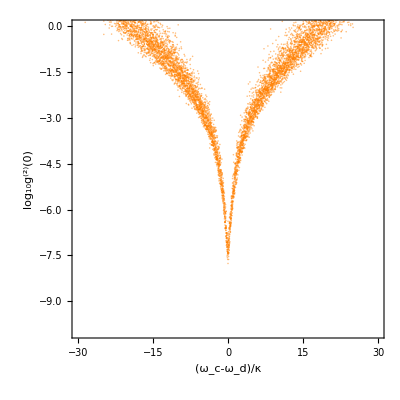

```mathematica
datalist=Import["/home/u000011703749/2photonJ-Cdeltag&deltaz-5E0.3.txt","Table"];
ListPlot[datalist,FrameLabel->{"(ω_c-ω_d)/κ","log_10g^(2)(0)"},BaseStyle->{FontSize->20,FontFamily->"Calibri"},Joined->False,PlotStyle->{Orange,Opacity[0.5]},Frame->True,PlotRange->{{-30,30},{-10,0}},AspectRatio->1]
```

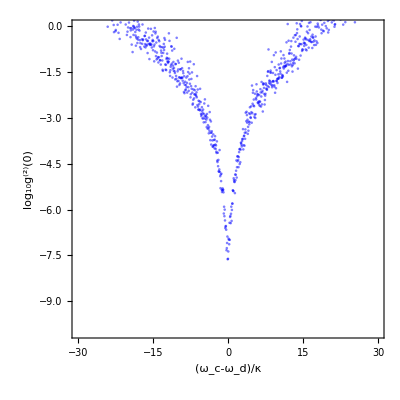

```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[100];



data=ParallelTable[
ωr=4*2*Pi;
ωq=8*2*Pi;
Na=10;


γ=0.001*ωr;
κ=0.001*ωr;
E1=0.03*κ;
max1=30*κ;
min1=-30*κ;      (*max and min value of Δ*)
segment1=1000;

Δ=N[min1+(max1-min1)*(m-1)/segment1];(*m is the variable of Δ for circulation*)
(*Δ=ωr-ωd*)
C1=√(E1^2/(2 E1^2+4 Δ^2+κ^2));
ωqdeviation=10^-5*ωq;
gdelta=RandomReal[{0,0.02*ωr},Na];
deltadata=RandomReal[NormalDistribution[ωq,ωqdeviation],Na]-ωq;

equs=Table[{deltadata[[i]]*ToExpression[StringJoin["C2",ToString[i]]]+gdelta[[i]]*C2*√2+E1/2*ToExpression[StringJoin["C3",ToString[i]]]-I/2*γ*ToExpression[StringJoin["C2",ToString[i]]]+2*Δ*ToExpression[StringJoin["C2",ToString[i]]]==0,deltadata[[i]]*ToExpression[StringJoin["C3",ToString[i]]]+gdelta[[i]]*C3*√6+E1/2*ToExpression[StringJoin["C2",ToString[i]]]-I/2*κ*ToExpression[StringJoin["C3",ToString[i]]]-I/2*γ*ToExpression[StringJoin["C3",ToString[i]]]+Δ*ToExpression[StringJoin["C3",ToString[i]]]+2*Δ*ToExpression[StringJoin["C3",ToString[i]]]==0},{i,1,Na}];
equs=Flatten[equs];
equs=Append[equs,(Sum[gdelta[[i]]*√2*ToExpression[StringJoin["C2",ToString[i]]],{i,Na}])+E1/2*C1*√2+E1/2*C3*√3-I*κ*C2+2*Δ*C2==0];
equs=Append[equs,(Sum[gdelta[[i]]*√6*ToExpression[StringJoin["C3",ToString[i]]],{i,Na}])+E1/2*C2*√3-I/2*κ*C3*3+3*Δ*C3==0];

vars={C2,C3,Table[ToExpression[StringJoin["C2",ToString[i]]],{i,1,Na}],Table[ToExpression[StringJoin["C3",ToString[i]]],{i,1,Na}]};
vars=Flatten[vars];
S=NSolve[equs,vars];
C2data=C2/.S[[1,1]];
C3data=C3/.S[[1,2]];
logg20=Log10[(Abs[C2data]^2*2+Abs[C3data]^2*6)/((E1^2/(2 E1^2+4 Δ^2+κ^2))^2)];


{Δ/κ,logg20},{m,1,1000+1,1},Method->"FinestGrained"

];
(*Circulation is ended.*)


ListPlot[data,FrameLabel->{"(ω_c-ω_d)/κ","log_10g^(2)(0)"},BaseStyle->{FontSize->20,FontFamily->"Calibri"},Joined->False,PlotStyle->{Blue,Opacity[0.5]},Frame->True,PlotRange->{{-30,30},{-10,0}},AspectRatio->1]
```

```mathematica
datalist=Import["/home/u000011703749/2photonJ-Cdeltag&deltaz-5E0.03.txt","Table"];
datalist=Join[datalist,data];
Export["/home/u000011703749/2photonJ-Cdeltag&deltaz-5E0.03.txt",datalist,"Table"];
```

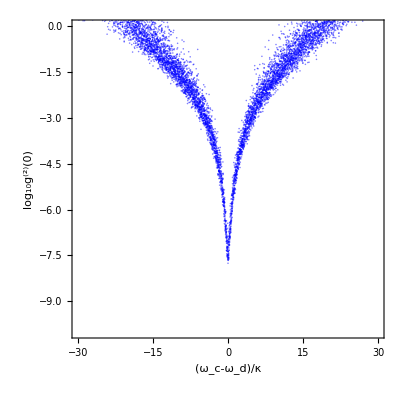

```mathematica
datalist=Import["/home/u000011703749/2photonJ-Cdeltag&deltaz-5E0.03.txt","Table"];
ListPlot[datalist,FrameLabel->{"(ω_c-ω_d)/κ","log_10g^(2)(0)"},BaseStyle->{FontSize->20,FontFamily->"Calibri"},Joined->False,PlotStyle->{Blue,Opacity[0.5]},Frame->True,PlotRange->{{-30,30},{-10,0}},AspectRatio->1]
```

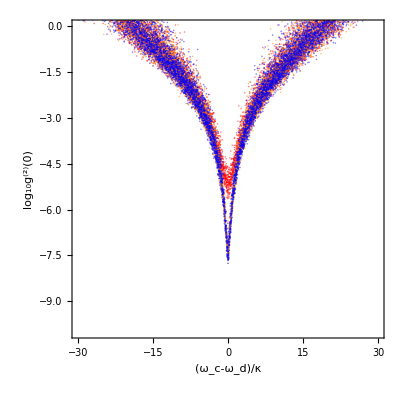

```mathematica
Show[-Graphics-,-Graphics-,-Graphics-]
```

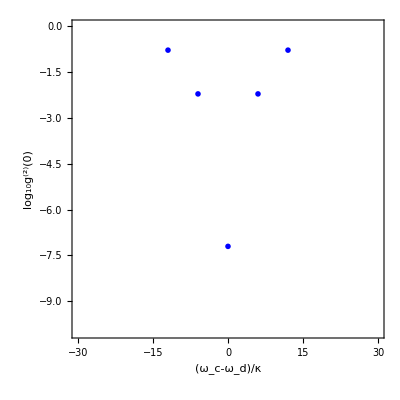

```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[100];



data=ParallelTable[
ωr=4*2*Pi;
ωq=8*2*Pi;
Na=10;


γ=0.001*ωr;
κ=0.001*ωr;
E1=0.03*κ;
max1=30*κ;
min1=-30*κ;      (*max and min value of Δ*)
segment1=10;

Δ=N[min1+(max1-min1)*(m-1)/segment1];(*m is the variable of Δ for circulation*)
(*Δ=ωr-ωd*)
C1=√(E1^2/(2 E1^2+4 Δ^2+κ^2));

g=0.01*ωr;


equs=Table[{g*C2*√2+E1/2*ToExpression[StringJoin["C3",ToString[i]]]-I/2*γ*ToExpression[StringJoin["C2",ToString[i]]]+2*Δ*ToExpression[StringJoin["C2",ToString[i]]]==0,g*C3*√6+E1/2*ToExpression[StringJoin["C2",ToString[i]]]-I/2*κ*ToExpression[StringJoin["C3",ToString[i]]]-I/2*γ*ToExpression[StringJoin["C3",ToString[i]]]+Δ*ToExpression[StringJoin["C3",ToString[i]]]+2*Δ*ToExpression[StringJoin["C3",ToString[i]]]==0},{i,1,Na}];
equs=Flatten[equs];
equs=Append[equs,(Sum[g*√2*ToExpression[StringJoin["C2",ToString[i]]],{i,Na}])+E1/2*C1*√2+E1/2*C3*√3-I*κ*C2+2*Δ*C2==0];
equs=Append[equs,(Sum[g*√6*ToExpression[StringJoin["C3",ToString[i]]],{i,Na}])+E1/2*C2*√3-I/2*κ*C3*3+3*Δ*C3==0];

vars={C2,C3,Table[ToExpression[StringJoin["C2",ToString[i]]],{i,1,Na}],Table[ToExpression[StringJoin["C3",ToString[i]]],{i,1,Na}]};
vars=Flatten[vars];
S=NSolve[equs,vars];
C2data=C2/.S[[1,1]];
C3data=C3/.S[[1,2]];
logg20=Log10[(Abs[C2data]^2*2+Abs[C3data]^2*6)/((E1^2/(2 E1^2+4 Δ^2+κ^2))^2)];


{Δ/κ,logg20},{m,1,10+1,1},Method->"FinestGrained"

];
(*Circulation is ended.*)


ListPlot[data,FrameLabel->{"(ω_c-ω_d)/κ","log_10g^(2)(0)"},BaseStyle->{FontSize->20,FontFamily->"Calibri"},Joined->False,PlotStyle->{Blue},PlotMarkers->"OpenMarkers",Frame->True,PlotRange->{{-30,30},{-10,0}},AspectRatio->1]
```

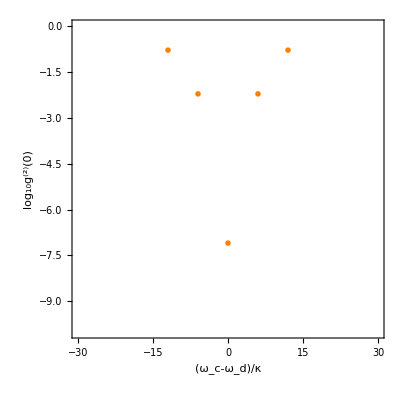

```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[100];



data=ParallelTable[
ωr=4*2*Pi;
ωq=8*2*Pi;
Na=10;


γ=0.001*ωr;
κ=0.001*ωr;
E1=0.3*κ;
max1=30*κ;
min1=-30*κ;      (*max and min value of Δ*)
segment1=10;

Δ=N[min1+(max1-min1)*(m-1)/segment1];(*m is the variable of Δ for circulation*)
(*Δ=ωr-ωd*)
C1=√(E1^2/(2 E1^2+4 Δ^2+κ^2));

g=0.01*ωr;


equs=Table[{g*C2*√2+E1/2*ToExpression[StringJoin["C3",ToString[i]]]-I/2*γ*ToExpression[StringJoin["C2",ToString[i]]]+2*Δ*ToExpression[StringJoin["C2",ToString[i]]]==0,g*C3*√6+E1/2*ToExpression[StringJoin["C2",ToString[i]]]-I/2*κ*ToExpression[StringJoin["C3",ToString[i]]]-I/2*γ*ToExpression[StringJoin["C3",ToString[i]]]+Δ*ToExpression[StringJoin["C3",ToString[i]]]+2*Δ*ToExpression[StringJoin["C3",ToString[i]]]==0},{i,1,Na}];
equs=Flatten[equs];
equs=Append[equs,(Sum[g*√2*ToExpression[StringJoin["C2",ToString[i]]],{i,Na}])+E1/2*C1*√2+E1/2*C3*√3-I*κ*C2+2*Δ*C2==0];
equs=Append[equs,(Sum[g*√6*ToExpression[StringJoin["C3",ToString[i]]],{i,Na}])+E1/2*C2*√3-I/2*κ*C3*3+3*Δ*C3==0];

vars={C2,C3,Table[ToExpression[StringJoin["C2",ToString[i]]],{i,1,Na}],Table[ToExpression[StringJoin["C3",ToString[i]]],{i,1,Na}]};
vars=Flatten[vars];
S=NSolve[equs,vars];
C2data=C2/.S[[1,1]];
C3data=C3/.S[[1,2]];
logg20=Log10[(Abs[C2data]^2*2+Abs[C3data]^2*6)/((E1^2/(2 E1^2+4 Δ^2+κ^2))^2)];


{Δ/κ,logg20},{m,1,10+1,1},Method->"FinestGrained"

];
(*Circulation is ended.*)


ListPlot[data,FrameLabel->{"(ω_c-ω_d)/κ","log_10g^(2)(0)"},BaseStyle->{FontSize->20,FontFamily->"Calibri"},Joined->False,PlotStyle->{Orange},PlotMarkers->"OpenMarkers",Frame->True,PlotRange->{{-30,30},{-10,0}},AspectRatio->1]
```

```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[100];



data=ParallelTable[
ωr=4*2*Pi;
ωq=8*2*Pi;
Na=10;


γ=0.001*ωr;
κ=0.001*ωr;
E1=3*κ;
max1=30*κ;
min1=-30*κ;      (*max and min value of Δ*)
segment1=10;

Δ=N[min1+(max1-min1)*(m-1)/segment1];(*m is the variable of Δ for circulation*)
(*Δ=ωr-ωd*)
C1=√(E1^2/(2 E1^2+4 Δ^2+κ^2));

g=0.01*ωr;


equs=Table[{g*C2*√2+E1/2*ToExpression[StringJoin["C3",ToString[i]]]-I/2*γ*ToExpression[StringJoin["C2",ToString[i]]]+2*Δ*ToExpression[StringJoin["C2",ToString[i]]]==0,g*C3*√6+E1/2*ToExpression[StringJoin["C2",ToString[i]]]-I/2*κ*ToExpression[StringJoin["C3",ToString[i]]]-I/2*γ*ToExpression[StringJoin["C3",ToString[i]]]+Δ*ToExpression[StringJoin["C3",ToString[i]]]+2*Δ*ToExpression[StringJoin["C3",ToString[i]]]==0},{i,1,Na}];
equs=Flatten[equs];
equs=Append[equs,(Sum[g*√2*ToExpression[StringJoin["C2",ToString[i]]],{i,Na}])+E1/2*C1*√2+E1/2*C3*√3-I*κ*C2+2*Δ*C2==0];
equs=Append[equs,(Sum[g*√6*ToExpression[StringJoin["C3",ToString[i]]],{i,Na}])+E1/2*C2*√3-I/2*κ*C3*3+3*Δ*C3==0];

vars={C2,C3,Table[ToExpression[StringJoin["C2",ToString[i]]],{i,1,Na}],Table[ToExpression[StringJoin["C3",ToString[i]]],{i,1,Na}]};
vars=Flatten[vars];
S=NSolve[equs,vars];
C2data=C2/.S[[1,1]];
C3data=C3/.S[[1,2]];
logg20=Log10[(Abs[C2data]^2*2+Abs[C3data]^2*6)/((E1^2/(2 E1^2+4 Δ^2+κ^2))^2)];


{Δ/κ,logg20},{m,1,10+1,1},Method->"FinestGrained"

];
(*Circulation is ended.*)


ListPlot[data,FrameLabel->{"(ω_c-ω_d)/κ","log_10g^(2)(0)"},BaseStyle->{FontSize->20,FontFamily->"Calibri"},Joined->False,PlotStyle->{Red},PlotMarkers->"OpenMarkers",Frame->True,PlotRange->{{-30,30},{-10,0}},AspectRatio->1]
```

-Graphics-

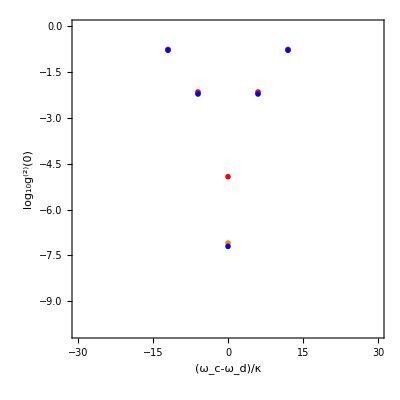

```mathematica
Show[-Graphics-,-Graphics-,-Graphics-]
```

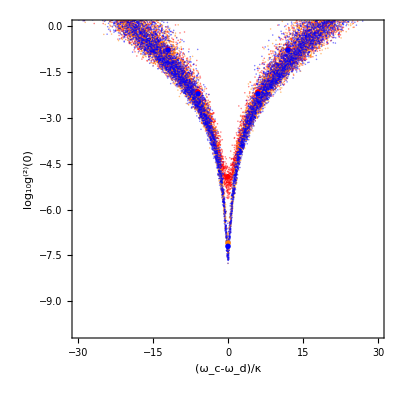

```mathematica
Show[-Graphics-,-Graphics-]
```

```mathematica
Export["/home/u000011703749/fig2b1.eps",-Graphics-]
```

/home/u000011703749/fig2b1.eps